```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

### Code

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% -- ARBITRARY! -- of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals -- IS THIS NECESSARY?! -- and return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
Clear[ReliableDistances];ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]];
If[$debug,Print["smallest node in net: ",eins]];
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10% *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
If[$debug,Print["OutDegreeRemaining (massaged): ", odr]];
z = Min[odr];  
If[$debug,Print["treating as zero (in odr): ", z]];
(* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
If[$debug,Print["using \"OutDegreeRemaining\" to find end of reliable data: ",
(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>{{g},{f},{h}})]];
pos=(odr /. {Longest[g___,1],f:Longest[z..,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);If[$debug,Print["Position of first untrustworthy node: ", pos]]; 
(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
If[$debug,Print["distances (uncut): ",distances]];
maxdistance=Min[distances⟦pos⟧];
If[$debug,Print["last distance we'll trust: ", maxdistance]];
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
%39[["Distance"]]
```

{0,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
ReliableDistances[%39]
```

{2,1,0,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

```mathematica
Range[Max[Complement[%52,{∞}]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}

```mathematica
Last[Last[Position[%52,#,{1}]]]& /@ %53
```

{2,1,5,4,7,6,9,8,11,10,13,12,15,14,17,16,19,18,21,20,23,22,25,24,27,26,29,28,31,30,33,32,35,34,37,36,39,38,41,40,43,42,45,44,47,46,49,48}

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtchlen,mtch}=(ptrn/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_,{5,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay, including a mtch of length mtchlen *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtchlen,mtch}=(rats/.{a:Repeated[_,{0,5}],brun:Longest[Repeated[b_?(#>1&),{3,∞}]],Repeated[_,{0,3}]}:>{Length[{a}],Length[{brun}],b});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay, including a mtch of length mtchlen *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k, dlay, (max) match length,(diff|ratio)mtch}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen,mtch},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, get details: k-averaging, after dlay, match of length mtchlen *)
{k,dlay,mtchlen,mtch}=ans⟦2⟧;
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldFirst];
GuessDimension[sss0_] := Module[{len,sss,ans,anssum,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];  (* already have Repeating or Dead Verdict *)

len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]
(* ,DistanceLastPositions[sss],DistanceTally[sss]  *) },
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];

While[len<5000 && anssum⟦1,-1⟧<10+5*Length[anssum],(* try for agreement *)
chngd=True;
sss=SSSEvolve[sss,len*Round[(10+5*Length[anssum]-anssum⟦1,-1⟧)/5]];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
If[$debug,Print["evol len: ", len]];
ans=DeleteCases[
CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]
(* ,DistanceLastPositions[sss],DistanceTally[sss] *)  },
{"failed",___}];
(* extract dim & mtchlen, then sort in decreasing order by matchlen *)
anssum=ReverseSortBy[{#⟦1⟧,#⟦2,3⟧}& /@ ans,Last];  
(* gather by dim, total all matchlens *)
anssum={#⟦1,1⟧,Total[Last/@#]}& /@ GatherBy[anssum,First];
If[$debug,Print[anssum]];
];
vdct=If[Length[anssum]==1,anssum⟦1,1⟧ (* agree! *), anssum (* disagree *)];  
If[len<5000 , chngd=True; sss["Verdict"]=vdct]; (* trust it *)
If[chngd,sss0=sss; Print[vdct]]; (* update it if changed *)
ans
];
```

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

original functions:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
sss50=SSS[50,50,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];
sss90=SSS[90,20,SSSMax->20,NetSize->Medium,NetMethod->{NoSSS}];$debug=False;
```

```mathematica
$debug=False;
sss50⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]==sss50⟦"Net"⟧
```

Note the ambiguity here!  A different reduced form for this network would be:

```mathematica
{11·{{},{1,2,3}},{},{}},2·{{}},1·{{1,2,3}}
```

In fact, for doing the “offset and subtract” step, to identify dimension, the original, unreduced version is fine.  This is always true for 1-d networks, the reduced version becomes necessary for higher dimensions.

```mathematica
sss90⟦"Net"⟧
ToNetDifferenceSets[%]
ToReducedNetDifferenceSets[%]
FromNetDifferenceSets[%%]==sss90⟦"Net"⟧
```

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
nds=ToNetDifferenceSets[sss50⟦"Net"⟧]
```

{{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3},{},{},{},{1,2,3}}

Here an offset by 4 results in lots of 0s:

```mathematica
SetSubtract[nds⟦5;;-1⟧,nds⟦1;;-5⟧]
```

{{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0},{},{},{},{0,0,0}}

```mathematica
nds=ToNetDifferenceSets[sss90⟦"Net"⟧]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
SetSubtract[nds⟦2;;-1⟧,nds⟦1;;-2⟧]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
RecognizeNetSetDifferenceRow@ToNetDifferenceSets[sss90["Net"]]
```

{dim,{1,0,{1}}}

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
net3dNamed={1->2,1->3,1->4,2->5,2->6,2->7,3->6,3->8,3->9,4->7,4->9,4->10,5->11,5->12,5->13,6->12,6->14,6->15,7->13,7->15,7->16,8->14,8->17,8->18,9->15,9->18,9->19,10->16,10->19,10->20,11->21,11->22,11->23,12->22,12->24,12->25,13->23,13->25,13->26,14->24,14->27,14->28,15->25,15->28,15->29,16->26,16->29,16->30,17->27,17->31,17->32,18->28,18->32,18->33,19->29,19->33,19->34,20->30,20->34,20->35,21->36,21->37,21->38,22->37,22->39,22->40,23->38,23->40,23->41,24->39,24->42,24->43,25->40,25->43,25->44,26->41,26->44,26->45,27->42,27->46,27->47,28->43,28->47,28->48,29->44,29->48,29->49,30->45,30->49,30->50,31->46,31->51,31->52,32->47,32->52,32->53,33->48,33->53,33->54,34->49,34->54,34->55,35->50,35->55,35->56,36->57,36->58,36->59,37->58,37->60,37->61,38->59,38->61,38->62,39->60,39->63,39->64,40->61,40->64,40->65,41->62,41->65,41->66,42->63,42->67,42->68,43->64,43->68,43->69,44->65,44->69,44->70,45->66,45->70,45->71,46->67,46->72,46->73,47->68,47->73,47->74,48->69,48->74,48->75,49->70,49->75,49->76,50->71,50->76,50->77,51->72,51->78,51->79,52->73,52->79,52->80,53->74,53->80,53->81,54->75,54->81,54->82,55->76,55->82,55->83,56->77,56->83,56->84,57->85,57->86,57->87,58->86,58->88,58->89,59->87,59->89,59->90,60->88,60->91,60->92,61->89,61->92,61->93,62->90,62->93,62->94,63->91,63->95,63->96,64->92,64->96,64->97,65->93,65->97,65->98,66->94,66->98,66->99,67->95,67->100,67->101,68->96,68->101,68->102,69->97,69->102,69->103,70->98,70->103,70->104,71->99,71->104,71->105,72->100,72->106,72->107,73->101,73->107,73->108,74->102,74->108,74->109,75->103,75->109,75->110,76->104,76->110,76->111,77->105,77->111,77->112,78->106,78->113,78->114,79->107,79->114,79->115,80->108,80->115,80->116,81->109,81->116,81->117,82->110,82->117,82->118,83->111,83->118,83->119,84->112,84->119,84->120,85->121,85->122,85->123,86->122,86->124,86->125,87->123,87->125,87->126,88->124,88->127,88->128,89->125,89->128,89->129,90->126,90->129,90->130,91->127,91->131,91->132,92->128,92->132,92->133,93->129,93->133,93->134,94->130,94->134,94->135,95->131,95->136,95->137,96->132,96->137,96->138,97->133,97->138,97->139,98->134,98->139,98->140,99->135,99->140,99->141,100->136,100->142,100->143,101->137,101->143,101->144,102->138,102->144,102->145,103->139,103->145,103->146,104->140,104->146,104->147,105->141,105->147,105->148,106->142,106->149,106->150,107->143,107->150,107->151,108->144,108->151,108->152,109->145,109->152,109->153,110->146,110->153,110->154,111->147,111->154,111->155,112->148,112->155,112->156,113->149,113->157,113->158,114->150,114->158,114->159,115->151,115->159,115->160,116->152,116->160,116->161,117->153,117->161,117->162,118->154,118->162,118->163,119->155,119->163,119->164,120->156,120->164,120->165,121->166,121->167,121->168,122->167,122->169,122->170,123->168,123->170,123->171,124->169,124->172,124->173,125->170,125->173,125->174,126->171,126->174,126->175,127->172,127->176,127->177,128->173,128->177,128->178,129->174,129->178,129->179,130->175,130->179,130->180,131->176,131->181,131->182,132->177,132->182,132->183,133->178,133->183,133->184,134->179,134->184,134->185,135->180,135->185,135->186,136->181,136->187,136->188,137->182,137->188,137->189,138->183,138->189,138->190,139->184,139->190,139->191,140->185,140->191,140->192,141->186,141->192,141->193,142->187,142->194,142->195,143->188,143->195,143->196,144->189,144->196,144->197,145->190,145->197,145->198,146->191,146->198,146->199,147->192,147->199,147->200,148->193,148->200,148->201,149->194,149->202,149->203,150->195,150->203,150->204,151->196,151->204,151->205,152->197,152->205,152->206,153->198,153->206,153->207,154->199,154->207,154->208,155->200,155->208,155->209,156->201,156->209,156->210,157->202,157->211,157->212,158->203,158->212,158->213,159->204,159->213,159->214,160->205,160->214,160->215,161->206,161->215,161->216,162->207,162->216,162->217,163->208,163->217,163->218,164->209,164->218,164->219,165->210,165->219,165->220,166->221,166->222,166->223,167->222,167->224,167->225,168->223,168->225,168->226,169->224,169->227,169->228,170->225,170->228,170->229,171->226,171->229,171->230,172->227,172->231,172->232,173->228,173->232,173->233,174->229,174->233,174->234,175->230,175->234,175->235,176->231,176->236,176->237,177->232,177->237,177->238,178->233,178->238,178->239,179->234,179->239,179->240,180->235,180->240,180->241,181->236,181->242,181->243,182->237,182->243,182->244,183->238,183->244,183->245,184->239,184->245,184->246,185->240,185->246,185->247,186->241,186->247,186->248,187->242,187->249,187->250,188->243,188->250,188->251,189->244,189->251,189->252,190->245,190->252,190->253,191->246,191->253,191->254,192->247,192->254,192->255,193->248,193->255,193->256,194->249,194->257,194->258,195->250,195->258,195->259,196->251,196->259,196->260,197->252,197->260,197->261,198->253,198->261,198->262,199->254,199->262,199->263,200->255,200->263,200->264,201->256,201->264,201->265,202->257,202->266,202->267,203->258,203->267,203->268,204->259,204->268,204->269,205->260,205->269,205->270,206->261,206->270,206->271,207->262,207->271,207->272,208->263,208->272,208->273,209->264,209->273,209->274,210->265,210->274,210->275,211->266,211->276,211->277,212->267,212->277,212->278,213->268,213->278,213->279,214->269,214->279,214->280,215->270,215->280,215->281,216->271,216->281,216->282,217->272,217->282,217->283,218->273,218->283,218->284,219->274,219->284,219->285,220->275,220->285,220->286,221->287,221->288,221->289,222->288,222->290,222->291,223->289,223->291,223->292,224->290,224->293,224->294,225->291,225->294,225->295,226->292,226->295,226->296,227->293,227->297,227->298,228->294,228->298,228->299,229->295,229->299,229->300,230->296,230->300,230->301,231->297,231->302,231->303,232->298,232->303,232->304,233->299,233->304,233->305,234->300,234->305,234->306,235->301,235->306,235->307,236->302,236->308,236->309,237->303,237->309,237->310,238->304,238->310,238->311,239->305,239->311,239->312,240->306,240->312,240->313,241->307,241->313,241->314,242->308,242->315,242->316,243->309,243->316,243->317,244->310,244->317,244->318,245->311,245->318,245->319,246->312,246->319,246->320,247->313,247->320,247->321,248->314,248->321,248->322,249->315,249->323,249->324,250->316,250->324,250->325,251->317,251->325,251->326,252->318,252->326,252->327,253->319,253->327,253->328,254->320,254->328,254->329,255->321,255->329,255->330,256->322,256->330,256->331,257->323,257->332,257->333,258->324,258->333,258->334,259->325,259->334,259->335,260->326,260->335,260->336,261->327,261->336,261->337,262->328,262->337,262->338,263->329,263->338,263->339,264->330,264->339,264->340,265->331,265->340,265->341,266->332,266->342,266->343,267->333,267->343,267->344,268->334,268->344,268->345,269->335,269->345,269->346,270->336,270->346,270->347,271->337,271->347,271->348,272->338,272->348,272->349,273->339,273->349,273->350,274->340,274->350,274->351,275->341,275->351,275->352,276->342,276->353,276->354,277->343,277->354,277->355,278->344,278->355,278->356,279->345,279->356,279->357,280->346,280->357,280->358,281->347,281->358,281->359,282->348,282->359,282->360,283->349,283->360,283->361,284->350,284->361,284->362,285->351,285->362,285->363,286->352,286->363,286->364,287->365,287->366,287->367,288->366,288->368,288->369,289->367,289->369,289->370,290->368,290->371,290->372,291->369,291->372,291->373,292->370,292->373,292->374,293->371,293->375,293->376,294->372,294->376,294->377,295->373,295->377,295->378,296->374,296->378,296->379,297->375,297->380,297->381,298->376,298->381,298->382,299->377,299->382,299->383,300->378,300->383,300->384,301->379,301->384,301->385,302->380,302->386,302->387,303->381,303->387,303->388,304->382,304->388,304->389,305->383,305->389,305->390,306->384,306->390,306->391,307->385,307->391,307->392,308->386,308->393,308->394,309->387,309->394,309->395,310->388,310->395,310->396,311->389,311->396,311->397,312->390,312->397,312->398,313->391,313->398,313->399,314->392,314->399,314->400,315->393,315->401,315->402,316->394,316->402,316->403,317->395,317->403,317->404,318->396,318->404,318->405,319->397,319->405,319->406,320->398,320->406,320->407,321->399,321->407,321->408,322->400,322->408,322->409,323->401,323->410,323->411,324->402,324->411,324->412,325->403,325->412,325->413,326->404,326->413,326->414,327->405,327->414,327->415,328->406,328->415,328->416,329->407,329->416,329->417,330->408,330->417,330->418,331->409,331->418,331->419,332->410,332->420,332->421,333->411,333->421,333->422,334->412,334->422,334->423,335->413,335->423,335->424,336->414,336->424,336->425,337->415,337->425,337->426,338->416,338->426,338->427,339->417,339->427,339->428,340->418,340->428,340->429,341->419,341->429,341->430,342->420,342->431,342->432,343->421,343->432,343->433,344->422,344->433,344->434,345->423,345->434,345->435,346->424,346->435,346->436,347->425,347->436,347->437,348->426,348->437,348->438,349->427,349->438,349->439,350->428,350->439,350->440,351->429,351->440,351->441,352->430,352->441,352->442,353->431,353->443,353->444,354->432,354->444,354->445,355->433,355->445,355->446,356->434,356->446,356->447,357->435,357->447,357->448,358->436,358->448,358->449,359->437,359->449,359->450,360->438,360->450,360->451,361->439,361->451,361->452,362->440,362->452,362->453,363->441,363->453,363->454,364->442,364->454,364->455,365->456,365->457,365->458,366->457,366->459,366->460,367->458,367->460,367->461,368->459,368->462,368->463,369->460,369->463,369->464,370->461,370->464,370->465,371->462,371->466,371->467,372->463,372->467,372->468,373->464,373->468,373->469,374->465,374->469,374->470,375->466,375->471,375->472,376->467,376->472,376->473,377->468,377->473,377->474,378->469,378->474,378->475,379->470,379->475,379->476,380->471,380->477,380->478,381->472,381->478,381->479,382->473,382->479,382->480,383->474,383->480,383->481,384->475,384->481,384->482,385->476,385->482,385->483,386->477,386->484,386->485,387->478,387->485,387->486,388->479,388->486,388->487,389->480,389->487,389->488,390->481,390->488,390->489,391->482,391->489,391->490,392->483,392->490,392->491,393->484,393->492,393->493,394->485,394->493,394->494,395->486,395->494,395->495,396->487,396->495,396->496,397->488,397->496,397->497,398->489,398->497,398->498,399->490,399->498,399->499,400->491,400->499,400->500,401->492,401->501,401->502,402->493,402->502,402->503,403->494,403->503,403->504,404->495,404->504,404->505,405->496,405->505,405->506,406->497,406->506,406->507,407->498,407->507,407->508,408->499,408->508,408->509,409->500,409->509,409->510,410->501,410->511,410->512,411->502,411->512,411->513,412->503,412->513,412->514,413->504,413->514,413->515,414->505,414->515,414->516,415->506,415->516,415->517,416->507,416->517,416->518,417->508,417->518,417->519,418->509,418->519,418->520,419->510,419->520,419->521,420->511,420->522,420->523,421->512,421->523,421->524,422->513,422->524,422->525,423->514,423->525,423->526,424->515,424->526,424->527,425->516,425->527,425->528,426->517,426->528,426->529,427->518,427->529,427->530,428->519,428->530,428->531,429->520,429->531,429->532,430->521,430->532,430->533,431->522,431->534,431->535,432->523,432->535,432->536,433->524,433->536,433->537,434->525,434->537,434->538,435->526,435->538,435->539,436->527,436->539,436->540,437->528,437->540,437->541,438->529,438->541,438->542,439->530,439->542,439->543,440->531,440->543,440->544,441->532,441->544,441->545,442->533,442->545,442->546,443->534,443->547,443->548,444->535,444->548,444->549,445->536,445->549,445->550,446->537,446->550,446->551,447->538,447->551,447->552,448->539,448->552,448->553,449->540,449->553,449->554,450->541,450->554,450->555,451->542,451->555,451->556,452->543,452->556,452->557,453->544,453->557,453->558,454->545,454->558,454->559,455->546,455->559,455->560};
```

```mathematica
Sort[Sort /@ ToNetDifferenceSets[net3dNamed]]
```

{{1,2,3},{3,4,5},{3,5,6},{3,5,6},{6,7,8},{6,8,9},{6,8,9},{6,9,10},{6,9,10},{6,9,10},{10,11,12},{10,12,13},{10,12,13},{10,13,14},{10,13,14},{10,13,14},{10,14,15},{10,14,15},{10,14,15},{10,14,15},{15,16,17},{15,17,18},{15,17,18},{15,18,19},{15,18,19},{15,18,19},{15,19,20},{15,19,20},{15,19,20},{15,19,20},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{15,20,21},{21,22,23},{21,23,24},{21,23,24},{21,24,25},{21,24,25},{21,24,25},{21,25,26},{21,25,26},{21,25,26},{21,25,26},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,26,27},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{21,27,28},{28,29,30},{28,30,31},{28,30,31},{28,31,32},{28,31,32},{28,31,32},{28,32,33},{28,32,33},{28,32,33},{28,32,33},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,33,34},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,34,35},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{28,35,36},{36,37,38},{36,38,39},{36,38,39},{36,39,40},{36,39,40},{36,39,40},{36,40,41},{36,40,41},{36,40,41},{36,40,41},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,41,42},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,42,43},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,43,44},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{36,44,45},{45,46,47},{45,47,48},{45,47,48},{45,48,49},{45,48,49},{45,48,49},{45,49,50},{45,49,50},{45,49,50},{45,49,50},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,50,51},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,51,52},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,52,53},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,53,54},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{45,54,55},{55,56,57},{55,57,58},{55,57,58},{55,58,59},{55,58,59},{55,58,59},{55,59,60},{55,59,60},{55,59,60},{55,59,60},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,60,61},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,61,62},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,62,63},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,63,64},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,64,65},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{55,65,66},{66,67,68},{66,68,69},{66,68,69},{66,69,70},{66,69,70},{66,69,70},{66,70,71},{66,70,71},{66,70,71},{66,70,71},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,71,72},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,72,73},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,73,74},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,74,75},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,75,76},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,76,77},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{66,77,78},{78,79,80},{78,80,81},{78,80,81},{78,81,82},{78,81,82},{78,81,82},{78,82,83},{78,82,83},{78,82,83},{78,82,83},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,83,84},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,84,85},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,85,86},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,86,87},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,87,88},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,88,89},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,89,90},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{78,90,91},{91,92,93},{91,93,94},{91,93,94},{91,94,95},{91,94,95},{91,94,95},{91,95,96},{91,95,96},{91,95,96},{91,95,96},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,96,97},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,97,98},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,98,99},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,99,100},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,100,101},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,101,102},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,102,103},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,103,104},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105},{91,104,105}}

```mathematica
ToReducedNetDifferenceSets[%]
```

```mathematica
{1·{{1,2,3}},
1·{{3,4,5}},2·{{3,5,6}},
1·{{6,7,8}},2·{{6,8,9}},3·{{6,9,10}},
1·{{10,11,12}},2·{{10,12,13}},3·{{10,13,14}},4·{{10,14,15}},
1·{{15,16,17}},2·{{15,17,18}},3·{{15,18,19}},4·{{15,19,20}},5·{{15,20,21}},
1·{{21,22,23}},2·{{21,23,24}},3·{{21,24,25}},4·{{21,25,26}},5·{{21,26,27}},6·{{21,27,28}},
1·{{28,29,30}},2·{{28,30,31}},3·{{28,31,32}},4·{{28,32,33}},5·{{28,33,34}},6·{{28,34,35}},7·{{28,35,36}},
1·{{36,37,38}},2·{{36,38,39}},3·{{36,39,40}},4·{{36,40,41}},5·{{36,41,42}},6·{{36,42,43}},7·{{36,43,44}},8·{{36,44,45}},
1·{{45,46,47}},2·{{45,47,48}},3·{{45,48,49}},4·{{45,49,50}},5·{{45,50,51}},6·{{45,51,52}},7·{{45,52,53}},8·{{45,53,54}},9·{{45,54,55}},
1·{{55,56,57}},2·{{55,57,58}},3·{{55,58,59}},4·{{55,59,60}},5·{{55,60,61}},6·{{55,61,62}},7·{{55,62,63}},8·{{55,63,64}},9·{{55,64,65}},10·{{55,65,66}},
1·{{66,67,68}},2·{{66,68,69}},3·{{66,69,70}},4·{{66,70,71}},5·{{66,71,72}},6·{{66,72,73}},7·{{66,73,74}},8·{{66,74,75}},9·{{66,75,76}},10·{{66,76,77}},11·{{66,77,78}},
1·{{78,79,80}},2·{{78,80,81}},3·{{78,81,82}},4·{{78,82,83}},5·{{78,83,84}},6·{{78,84,85}},7·{{78,85,86}},8·{{78,86,87}},9·{{78,87,88}},10·{{78,88,89}},11·{{78,89,90}},12·{{78,90,91}},
1·{{91,92,93}},2·{{91,93,94}},3·{{91,94,95}},4·{{91,95,96}},5·{{91,96,97}},6·{{91,97,98}},7·{{91,98,99}},8·{{91,99,100}},9·{{91,100,101}},10·{{91,101,102}},11·{{91,102,103}},12·{{91,103,104}},13·{{91,104,105}}}
```

```mathematica
rs
```

<|Index→1627526,QCode→242423434,RuleSet→{A→B,B→ABB}|>

```mathematica
rs
```

```mathematica
rs
```

```mathematica
%39[["RuleSet"]]
```

{AB→,→BAA}

```mathematica
%39[["Evolution"]][[4]]
```

BAABAAA

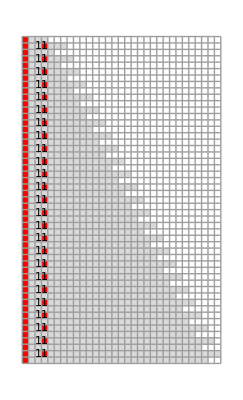

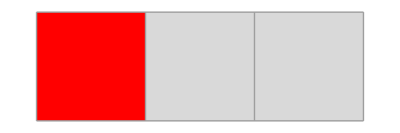
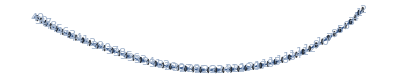
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"AB"->"",""->"BAA"},"BAAA",50];
```

```mathematica
%60[["Verdict"]]
```

OK

```mathematica
CheckDimension@LeastUsedRulePositions[%69]
CheckDimension@MaxStateLengthPositions[%69]
CheckDimension@DistanceTally[%69]
```

{1D,{1,0,24,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

{1D,{1,0,23,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

{1D,{1,0,47,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

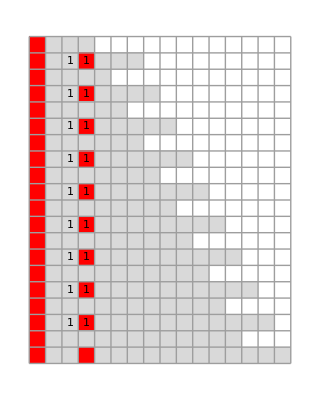
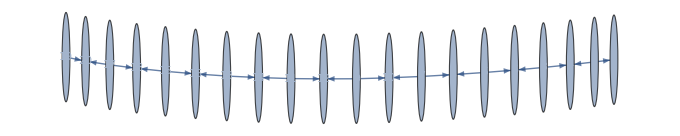
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[%69,Max->20,ImageSize->100,NetSize->500]
```

```mathematica
$debug=True
```

True

```mathematica
Sort@%69["Net"]
```

{1→2,1→4,3→4,3→6,5→6,5→8,7→8,7→10,9→10,9→12,11→12,11→14,13→14,13→16,15→16,15→18,17→18,17→20,19→20,19→22,21→22,21→24,23→24,23→26,25→26,25→28,27→28,27→30,29→30,29→32,31→32,31→34,33→34,33→36,35→36,35→38,37→38,37→40,39→40,39→42,41→42,41→44,43→44,43→46,45→46,45→48,47→48,47→50,49→50}

```mathematica
ToNetDifferenceSets@Sort@%69["Net"]
```

{{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1,3},{},{1}}

```mathematica
ToReducedNetDifferenceSets@%
```

{24·{{1,3},{}},{1}}

Note:  That took an inordinately long time to do a very simple reduction.  We should never use ToReducedNetDifferenceSets for 1-d cases, since shift & subtract already works perfectly with all of them, and ToReducedNetDifferenceSets may be really slow.

```mathematica
%69["Distance"]
```

{0,1,∞,1,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

```mathematica
ReliableDistances[%69]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {0,1,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

last distance we'll trust: ∞

{0,1,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

```mathematica
DistanceLastPositions[%69]
```

smallest node in net: 1

OutDegreeRemaining (massaged): {∞,∞,∞,∞,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2,0}

treating as zero (in odr): 0

using "OutDegreeRemaining" to find end of reliable data: {{∞,∞,∞,∞,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,2},{0},{}}

Position of first untrustworthy node: {}

distances (uncut): {0,1,2,1,4,3,6,5,8,7,10,9,12,11,14,13,16,15,18,17,20,19,22,21,24,23,26,25,28,27,30,29,32,31,34,33,36,35,38,37,40,39,42,41,44,43,46,45,48,47}

last distance we'll trust: ∞

Part::take: Cannot take positions 50 through 48 in {2,1,2,1,2,1,2,1,2,1,«40»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

## Loop to find & compare data for 3-D cases

```mathematica
rs
```

```mathematica
rs
```

```mathematica
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
sums={};
```

```mathematica
While[rs["Index"]<10^10,                         (* or some other large number *)
(* Print[rs["Index"]]; *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans,  (* skip all possible *)

sss=SSS[rs["RuleSet"],50,Mode->Silent]; 
MatchQ[sss["Verdict"],"Dead"|"Repeating"], rs=FromReducedRankIndex[rs["Index"]+1],

sss=SSS[rs["RuleSet"],sss["Evolution"][[25]],100,Mode->Silent];  (* restart from position 25, going 100 steps *)
MatchQ[sss["Verdict"],"Dead"|"Repeating"], rs=FromReducedRankIndex[rs["Index"]+1],

MemberQ[CheckDimension@LeastUsedRulePositions[sss],"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[CheckDimension@MaxStateLengthPositions[sss],"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[CheckDimension@DistanceLastPositions[sss],"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[CheckDimension@DistanceTally[sss],"1D"|"2D"],rs=FromReducedRankIndex[rs["Index"]+1],

sss=SSSEvolve[sss,750];  (* going 750 additional steps *)
MatchQ[sss["Verdict"],"Dead"|"Repeating"], rs=FromReducedRankIndex[rs["Index"]+1],

MemberQ[sums[[1]]=CheckDimension@LeastUsedRulePositions[sss],"1D"|"2D"|"exp"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[sums[[2]]=CheckDimension@MaxStateLengthPositions[sss],"1D"|"2D"|"exp"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[sums[[3]]=CheckDimension@DistanceLastPositions[sss],"1D"|"2D"|"exp"],rs=FromReducedRankIndex[rs["Index"]+1],
MemberQ[sums[[4]]=CheckDimension@DistanceTally[sss],"1D"|"2D"|"exp"],rs=FromReducedRankIndex[rs["Index"]+1],

Length@Union[sss["RulesUsed"]]<Length@sss["RuleSet"],
Print["rs: ",rs,": unused rules: ",Complement[Range[Length@sss["RuleSet"]],sss["RuleSet"]]];rs=FromReducedRankIndex[rs["Index"]+1],

True,
Print[rs ," : ",sums, " - ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->25,SSSSize->{150,150},NetMax->25,NetSize->{350,150},VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
Print@SSSDisplay[sss,NetMethod->{NoSSS,GraphPlot},NetSize->{450,150},VertexLabels->Placed[Automatic,Tooltip]];rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
]
```

1

2

3

4

5

6

7

10

11

12

16

17

18

20

21

22

23

24

25

26

27

32

50

51

52

55

56

57

60

77

78

79

80

81

82

90

97

98

102

103

104

105

106

107

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

135

157

250

251

252

255

256

257

275

276

277

280

282

300

382

385

386

387

391

392

393

394

395

396

397

401

402

407

450

482

490

507

515

516

517

521

522

523

526

527

528

532

550

551

552

555

556

557

560

561

562

566

567

568

570

571

572

576

577

578

579

580

581

582

590

591

592

593

594

595

596

597

598

600

601

602

603

604

605

606

607

610

611

612

613

614

615

616

617

618

619

620

621

622

623

624

625

626

627

628

629

630

631

632

635

636

637

638

639

640

641

642

643

644

645

646

647

648

649

650

651

652

657

675

782

1250

1251

1252

1255

1256

1257

1275

1276

1277

1280

1282

1375

1376

1377

1380

1381

1382

1400

1407

1500

1907

1925

1926

1927

1930

1931

1932

1935

1952

1956

1957

1965

1966

1967

1971

1972

1973

1974

1975

1976

1977

1978

1980

1981

1982

1985

2002

2003

2004

2005

2006

2007

2010

2032

2250

2407

2450

2532

2575

2576

2577

2580

2581

2582

2585

2602

2603

2604

2605

2606

2607

2615

2627

2628

2629

2630

2631

2632

2640

2657

2750

2751

2752

2755

2756

2757

2775

2776

2777

2780

2782

2800

2801

2802

2805

2806

2807

2810

2827

2828

2829

2830

2831

2832

2840

2847

2848

2849

2850

2851

2852

2853

2854

2855

2856

2857

2860

2877

2878

2879

2880

2881

2882

2885

2886

2887

2888

2889

2890

2891

2892

2893

2894

2895

2896

2897

2898

2899

2900

2901

2902

2907

2950

2951

2952

2955

2956

2957

2960

2961

2962

2966

2967

2968

2970

2971

2972

2976

2977

2978

2979

2980

2981

2982

2990

2997

2998

3002

3003

3004

3005

3006

3007

3015

3016

3017

3018

3019

3020

3021

3022

3023

3024

3025

3026

3027

3028

3032

3050

3051

3052

3055

3056

3057

3060

3061

3062

3066

3067

3068

3070

3071

3072

3073

3074

3075

3076

3077

3078

3079

3080

3081

3082

3090

3091

3092

3093

3094

3095

3096

3097

3098

3099

3100

3101

3102

3103

3104

3105

3106

3107

3110

3111

3112

3113

3114

3115

3116

3117

3118

3119

3120

3121

3122

3123

3124

3125

3126

3127

3128

3129

3130

3131

3132

3135

3136

3137

3138

3139

3140

3141

3142

3143

3144

3145

3146

3147

3148

3149

3150

3151

3152

3157

3175

3176

3177

3180

3181

3182

3185

3186

3187

3191

3192

3193

3195

3196

3197

3198

3199

3200

3201

3202

3203

3204

3205

3206

3207

3215

3216

3217

3218

3219

3220

3221

3222

3223

3224

3225

3226

3227

3228

3229

3230

3231

3232

3235

3236

3237

3238

3239

3240

3241

3242

3243

3244

3245

3246

3247

3248

3249

3250

3251

3252

3253

3254

3255

3256

3257

3260

3282

3375

3907

6250

6251

6252

6255

6256

6257

6275

6276

6277

6280

6282

6375

6376

6377

6380

6381

6382

6400

6407

6875

6876

6877

6880

6881

6882

6900

6901

6902

6905

6906

6907

7000

7032

7500

9532

9625

9626

9627

9630

9631

9632

9650

9651

9652

9655

9656

9657

9675

9757

9760

9777

9778

9779

9780

9781

9782

9825

9826

9827

9830

9831

9832

9835

9852

9856

9857

9865

9866

9867

9871

9872

9873

9874

9875

9876

9877

9878

9879

9880

9881

9882

9890

9897

9898

9899

9900

9901

9902

9903

9904

9905

9906

9907

9925

10007

10010

10011

10012

10016

10017

10018

10019

10020

10021

10022

10026

10027

10028

10029

10030

10031

10032

10050

10157

11250

12032

12250

12657

12875

12876

12877

12880

12881

12882

12900

12901

12902

12905

12906

12907

12925

13007

13010

13011

13012

13016

13017

13018

13019

13020

13021

13022

13026

13027

13028

13029

13030

13031

13032

13075

13132

13140

13141

13142

13146

13147

13148

13151

13152

13153

13154

13155

13156

13157

13200

13282

13750

13751

13752

13755

13756

13757

13775

13776

13777

13780

13782

13875

13876

13877

13880

13881

13882

13900

13907

14000

14001

14002

14005

14006

14007

14025

14026

14027

14030

14032

14050

14132

14135

14136

14137

14141

14142

14143

14144

14145

14146

14147

14151

14152

14157

14200

14232

14240

14241

14242

14246

14247

14248

14249

14250

14251

14252

14253

14254

14255

14256

14257

14265

14266

14267

14271

14272

14273

14274

14275

14276

14277

14278

14282

14300

14382

14385

14386

14387

14388

14389

14390

14391

14392

14393

14394

14395

14396

14397

14398

14399

14400

14401

14402

14407

14425

14426

14427

14430

14431

14432

14435

14436

14437

14441

14442

14443

14445

14446

14447

14451

14452

14456

14457

14465

14466

14467

14468

14469

14470

14471

14472

14473

14474

14475

14476

14477

14478

14480

14481

14482

14485

14486

14487

14488

14489

14490

14491

14492

14493

14494

14495

14496

14497

14501

14502

14503

14504

14505

14506

14507

14510

14532

14750

14751

14752

14755

14756

14757

14775

14776

14777

14780

14782

14800

14801

14802

14805

14806

14807

14810

14827

14828

14829

14830

14831

14832

14840

14847

14848

14849

14850

14851

14852

14853

14854

14855

14856

14857

14860

14877

14878

14879

14880

14881

14882

14885

14886

14887

14888

14889

14890

14891

14892

14893

14894

14895

14896

14897

14898

14899

14900

14901

14902

14907

14950

14982

14990

15007

15015

15016

15017

15018

15019

15020

15021

15022

15023

15024

15025

15026

15027

15028

15032

15075

15076

15077

15080

15081

15082

15085

15086

15087

15091

15092

15093

15095

15096

15097

15101

15102

15103

15104

15105

15106

15107

15115

15116

15117

15118

15119

15120

15121

15122

15123

15126

15127

15128

15129

15130

15131

15132

15140

15157

15250

15251

15252

15255

15256

15257

15275

15276

15277

15280

15282

15300

15301

15302

15305

15306

15307

15310

15327

15328

15329

15330

15331

15332

15340

15347

15348

15349

15350

15351

15352

15353

15354

15355

15356

15357

15360

15361

15362

15363

15364

15365

15366

15367

15368

15369

15370

15371

15372

15376

15377

15378

15379

15380

15381

15382

15385

15386

15387

15388

15389

15390

15391

15392

15393

15394

15395

15396

15397

15398

15399

15400

15401

15402

15407

15450

15451

15452

15455

15456

15457

15460

15461

15462

15466

15467

15468

15470

15471

15472

15473

15474

15475

15476

15477

15478

15479

15480

15481

15482

15490

15491

15492

15493

15494

15495

15496

15497

15498

15500

15501

15502

15503

15504

15505

15506

15507

15515

15516

15517

15518

15519

15520

15521

15522

15523

15524

15525

15526

15527

15528

15532

15550

15551

15552

15555

15556

15557

15560

15561

15562

15566

15567

15568

15570

15571

15572

15573

15574

15575

15576

15577

15578

15579

15580

15581

15582

15590

15591

15592

15593

15594

15595

15596

15597

15598

15599

15600

15601

15602

15603

15604

15605

15606

15607

15610

15611

15612

15613

15614

15615

15616

15617

15618

15619

15620

15621

15622

15623

15624

15625

15626

15627

15628

15629

15630

15631

15632

15635

15636

15637

15638

15639

15640

15641

15642

15643

15644

15645

15646

15647

15648

15649

15650

15651

15652

15657

15675

15676

15677

15680

15681

15682

15685

15686

15687

15691

15692

15693

15695

15696

15697

15698

15699

15700

15701

15702

15703

15704

15705

15706

15707

15715

15716

15717

15718

15719

15720

15721

15722

15723

15724

15725

15726

15727

15728

15729

15730

15731

15732

15735

15736

15737

15738

15739

15740

15741

15742

15743

15744

15745

15746

15747

15748

15749

15750

15751

15752

15753

15754

15755

15756

15757

15760

15782

15875

15876

15877

15880

15881

15882

15900

15901

15902

15905

15906

15907

15925

15926

15927

15930

15931

15932

15935

15952

15953

15954

15955

15956

15957

15965

15972

15973

15974

15975

15976

15977

15978

15979

15980

15981

15982

15985

15986

15987

15988

15989

15990

15991

15992

15993

15994

15995

15996

15997

15998

15999

16000

16001

16002

16006

16007

16010

16011

16012

16013

16014

16015

16016

16017

16018

16019

16020

16021

16022

16023

16024

16025

16026

16027

16028

16029

16030

16031

16032

16075

16076

16077

16080

16081

16082

16085

16086

16087

16091

16092

16093

16095

16096

16097

16098

16099

16100

16101

16102

16103

16104

16105

16106

16107

16115

16116

16117

16118

16119

16120

16121

16122

16123

16124

16125

16126

16127

16128

16130

16131

16132

16140

16141

16142

16143

16144

16145

16146

16147

16148

16149

16150

16151

16152

16153

16154

16155

16156

16157

16175

16176

16177

16180

16181

16182

16185

16186

16187

16191

16192

16193

16195

16196

16197

16198

16199

16200

16201

16202

16203

16204

16205

16206

16207

16215

16216

16217

16218

16219

16220

16221

16222

16223

16224

16225

16226

16227

16228

16229

16230

16231

16232

16235

16236

16237

16238

16239

16240

16241

16242

16243

16244

16245

16246

16247

16248

16249

16250

16251

16252

16253

16254

16255

16256

16257

16260

16261

16262

16263

16264

16265

16266

16267

16268

16269

16270

16271

16272

16273

16274

16275

16276

16277

16278

16279

16280

16281

16282

16300

16407

16875

19532

31250

31251

31252

31255

31256

31257

31275

31276

31277

31280

31282

31375

31376

31377

31380

31381

31382

31400

31407

31875

31876

31877

31880

31881

31882

31900

31901

31902

31905

31906

31907

32000

32032

34375

34376

34377

34380

34381

34382

34400

34401

34402

34405

34406

34407

34500

34501

34502

34505

34506

34507

34525

34526

34527

34530

34532

35000

35157

37500

47657

48125

48126

48127

48130

48131

48132

48150

48151

48152

48155

48156

48157

48250

48251

48252

48255

48256

48257

48275

48276

48277

48280

48282

48375

48782

48800

48882

48885

48886

48887

48891

48892

48893

48894

48895

48896

48897

48901

48902

48907

49125

49126

49127

49130

49131

49132

49150

49151

49152

49155

49156

49157

49175

49257

49260

49277

49278

49279

49280

49281

49282

49325

49326

49327

49330

49331

49332

49335

49352

49356

49357

49365

49366

49367

49371

49372

49373

49374

49375

49376

49377

49378

49379

49380

49381

49382

49390

49391

49392

49396

49397

49398

49399

49400

49401

49402

49403

49404

49405

49406

49407

49450

49482

49490

49491

49492

49496

49497

49498

49499

49500

49501

49502

49503

49504

49505

49506

49507

49515

49516

49517

49521

49522

49523

49524

49525

49526

49527

49528

49532

49625

50032

50050

50051

50052

50055

50056

50057

50060

50077

50078

50079

50080

50081

50082

50090

50091

50092

50096

50097

50098

50099

50100

50101

50102

50103

50104

50105

50106

50107

50110

50127

50128

50129

50130

50131

50132

50135

50136

50137

50141

50142

50143

50144

50145

50146

50147

50151

50152

50157

50250

50782

56250

60157

61250

63282

64375

64376

64377

64380

64381

64382

64400

64401

64402

64405

64406

64407

64500

64501

64502

64505

64506

64507

64525

64526

64527

64530

64532

64625

65032

65050

65051

65052

65055

65056

65057

65060

65077

65081

65082

65090

65091

65092

65096

65097

65098

65099

65100

65101

65102

65103

65105

65106

65107

65110

65127

65128

65129

65130

65131

65132

65135

65136

65137

65141

65142

65143

65144

65145

65146

65147

65151

65152

65157

65375

65657

65700

65701

65702

65705

65706

65707

65710

65727

65728

65729

65730

65731

65732

65740

65752

65753

65754

65755

65756

65757

65765

65766

65767

65771

65772

65773

65776

65777

65778

65782

66000

66407

68750

68751

68752

68755

68756

68757

68775

68776

68777

68780

68782

68875

68876

68877

68880

68881

68882

68900

68907

69375

69376

69377

69380

69381

69382

69400

69401

69402

69405

69406

69407

69500

69532

70000

70001

70002

70005

70006

70007

70025

70026

70027

70030

70032

70125

70126

70127

70130

70131

70132

70150

70157

70250

70657

70675

70676

70677

70680

70681

70682

70685

70702

70706

70707

70715

70716

70717

70721

70722

70723

70724

70725

70726

70727

70728

70730

70731

70732

70735

70752

70753

70754

70755

70756

70757

70760

70782

71000

71157

71200

71201

71202

71205

71206

71207

71210

71227

71228

71229

71230

71231

71232

71240

71241

71242

71246

71247

71248

71249

71250

71251

71252

71253

71254

71255

71256

71257

71265

71266

71267

71271

71272

71273

71274

71275

71276

71277

71278

71282

71325

71326

71327

71330

71331

71332

71335

71352

71353

71354

71355

71356

71357

71365

71366

71367

71371

71372

71373

71374

71375

71376

71377

71378

71379

71380

71381

71382

71390

71407

71500

71907

71925

71926

71927

71930

71931

71932

71935

71936

71937

71941

71942

71943

71945

71946

71947

71951

71952

71953

71954

71955

71956

71957

71965

71966

71967

71968

71969

71970

71971

71972

71973

71974

71975

71976

71977

71978

71979

71980

71981

71982

71985

71986

71987

71988

71989

71990

71991

71992

71993

71994

71995

71996

71997

72001

72002

72003

72004

72005

72006

72007

72010

72032

72125

72126

72127

72130

72131

72132

72150

72151

72152

72155

72156

72157

72175

72176

72177

72180

72181

72182

72185

72202

72206

72207

72215

72222

72223

72224

72225

72226

72227

72228

72229

72230

72231

72232

72235

72252

72256

72257

72260

72277

72278

72279

72280

72281

72282

72325

72326

72327

72330

72331

72332

72335

72336

72337

72341

72342

72343

72345

72346

72347

72351

72352

72356

72357

72365

72366

72367

72368

72369

72370

72371

72372

72373

72374

72375

72376

72377

72378

72379

72380

72381

72382

72390

72397

72398

72399

72400

72401

72402

72403

72404

72405

72406

72407

72425

72426

72427

72430

72431

72432

72435

72436

72437

72441

72442

72443

72445

72446

72447

72451

72452

72453

72454

72455

72456

72457

72465

72466

72467

72468

72469

72470

72471

72472

72473

72474

72475

72476

72477

72478

72479

72480

72481

72482

72485

72502

72503

72504

72505

72506

72507

72510

72511

72512

72513

72514

72515

72516

72517

72518

72519

72520

72521

72522

72523

72524

72525

72526

72527

72528

72529

72530

72531

72532

72550

72657

73750

73751

73752

73755

73756

73757

73775

73776

73777

73780

73782

73875

73876

73877

73880

73881

73882

73900

73907

74000

74001

74002

74005

74006

74007

74025

74026

74027

74030

74032

74050

74132

74135

74136

74137

74141

74142

74143

74144

74145

74146

74147

74151

74152

74157

74200

74232

74240

74241

74242

74246

74247

74248

74249

74250

74251

74252

74253

74254

74255

74256

74257

74265

74266

74267

74271

74272

74273

74274

74275

74276

74277

74278

74282

74300

74382

74385

74386

74387

74388

74389

74390

74391

74392

74393

74394

74395

74396

74397

74398

74399

74400

74401

74402

74407

74425

74426

74427

74430

74431

74432

74435

74436

74437

74441

74442

74443

74445

74446

74447

74451

74452

74456

74457

74465

74466

74467

74468

74469

74470

74471

74472

74473

74474

74475

74476

74477

74478

74480

74481

74482

74485

74486

74487

74488

74489

74490

74491

74492

74493

74494

74495

74496

74497

74501

74502

74503

74504

74505

74506

74507

74510

74532

74750

74907

74950

75032

75075

75076

75077

75080

75081

75082

75085

75086

75087

75091

75092

75093

75095

75096

75097

75101

75102

75103

75104

75105

75106

75107

75115

75116

75117

75118

75119

75120

75121

75122

75123

75126

75127

75128

75129

75130

75131

75132

75140

75157

75375

75376

75377

75380

75381

75382

75400

75401

75402

75405

75406

75407

75425

75426

75427

75430

75431

75432

75435

75452

75453

75454

75455

75456

75457

75465

75472

75473

75474

75475

75476

75477

75478

75479

75480

75481

75482

75485

75502

75503

75504

75505

75506

75507

75510

75511

75512

75513

75514

75515

75516

75517

75518

75519

75520

75521

75522

75523

75524

75525

75526

75527

75528

75529

75530

75531

75532

75575

75576

75577

75580

75581

75582

75585

75586

75587

75591

75592

75593

75595

75596

75597

75601

75602

75603

75604

75605

75606

75607

75615

75627

75628

75629

75630

75631

75632

75640

75641

75642

75643

75644

75645

75646

75647

75648

75649

75650

75651

75652

75653

75654

75655

75656

75657

75700

75782

76250

76251

76252

76255

76256

76257

76275

76276

76277

76280

76282

76375

76376

76377

76380

76381

76382

76400

76407

76500

76501

76502

76505

76506

76507

76525

76526

76527

76530

76532

76550

76632

76635

76636

76637

76641

76642

76643

76644

76645

76646

76647

76651

76652

76657

76700

76732

76740

76741

76742

76746

76747

76748

76749

76750

76751

76752

76753

76754

76755

76756

76757

76765

76766

76767

76771

76772

76773

76774

76775

76776

76777

76778

76782

76800

76801

76802

76805

76806

76807

76810

76811

76812

76816

76817

76818

76820

76821

76822

76826

76827

76828

76829

76830

76831

76832

76840

76841

76842

76843

76844

76845

76846

76847

76848

76850

76851

76852

76853

76854

76855

76856

76857

76860

76877

76878

76879

76880

76881

76882

76885

76886

76887

76888

76889

76890

76891

76892

76893

76894

76895

76896

76897

76898

76899

76900

76901

76902

76907

76925

76926

76927

76930

76931

76932

76935

76936

76937

76941

76942

76943

76945

76946

76947

76948

76949

76950

76951

76952

76956

76957

76965

76966

76967

76968

76969

76970

76971

76972

76973

76974

76975

76976

76977

76978

76980

76981

76982

76985

76986

76987

76988

76989

76990

76991

76992

76993

76994

76995

76996

76997

76998

76999

77000

77001

77002

77003

77004

77005

77006

77007

77010

77032

77250

77251

77252

77255

77256

77257

77275

77276

77277

77280

77282

77300

77301

77302

77305

77306

77307

77310

77327

77328

77329

77330

77331

77332

77340

77347

77348

77349

77350

77351

77352

77353

77354

77355

77356

77357

77360

77361

77362

77363

77364

77365

77366

77367

77368

77369

77370

77371

77372

77376

77377

77378

77379

77380

77381

77382

77385

77386

77387

77388

77389

77390

77391

77392

77393

77394

77395

77396

77397

77398

77399

77400

77401

77402

77407

77450

77451

77452

77455

77456

77457

77460

77461

77462

77466

77467

77468

77470

77471

77472

77473

77474

77475

77476

77477

77478

77479

77480

77481

77482

77490

77497

77498

77502

77503

77504

77505

77506

77507

77515

77516

77517

77518

77519

77520

77521

77522

77523

77524

77525

77526

77527

77528

77532

77575

77576

77577

77580

77581

77582

77585

77586

77587

77591

77592

77593

77595

77596

77597

77598

77599

77600

77601

77602

77603

77604

77605

77606

77607

77615

77616

77617

77618

77619

77620

77621

77622

77623

77624

77625

77626

77627

77628

77629

77630

77631

77632

77640

77657

77750

77751

77752

77755

77756

77757

77775

77776

77777

77780

77782

77800

77801

77802

77805

77806

77807

77810

77827

77828

77829

77830

77831

77832

77840

77847

77848

77849

77850

77851

77852

77853

77854

77855

77856

77857

77860

77861

77862

77863

77864

77865

77866

77867

77868

77869

77870

77871

77872

77873

77874

77875

77876

77877

77878

77879

77880

77881

77882

77885

77886

77887

77888

77889

77890

77891

77892

77893

77894

77895

77896

77897

77898

77899

77900

77901

77902

77907

77950

77951

77952

77955

77956

77957

77960

77961

77962

77966

77967

77968

77970

77971

77972

77973

77974

77975

77976

77977

77978

77979

77980

77981

77982

77990

77991

77992

77993

77994

77995

77996

77997

77998

77999

78000

78001

78002

78003

78004

78005

78006

78007

78015

78016

78017

78018

78019

78020

78021

78022

78023

78024

78025

78026

78027

78028

78032

78050

78051

78052

78055

78056

78057

78060

78061

78062

78066

78067

78068

78070

78071

78072

78073

78074

78075

78076

78077

78078

78079

78080

78081

78082

78090

78091

78092

78093

78094

78095

78096

78097

78098

78099

78100

78101

78102

78103

78104

78105

78106

78107

78110

78111

78112

78113

78114

78115

78116

78117

78118

78119

78120

78121

78122

78123

78124

78125

78126

78127

78128

78129

78130

78131

78132

78135

78136

78137

78138

78139

78140

78141

78142

78143

78144

78145

78146

78147

78148

78149

78150

78151

78152

78157

78175

78176

78177

78180

78181

78182

78185

78186

78187

78191

78192

78193

78195

78196

78197

78198

78199

78200

78201

78202

78203

78204

78205

78206

78207

78215

78216

78217

78218

78219

78220

78221

78222

78223

78224

78225

78226

78227

78228

78229

78230

78231

78232

78235

78236

78237

78238

78239

78240

78241

78242

78243

78244

78245

78246

78247

78248

78249

78250

78251

78252

78253

78254

78255

78256

78257

78260

78282

78375

78376

78377

78380

78381

78382

78400

78401

78402

78405

78406

78407

78425

78426

78427

78430

78431

78432

78435

78452

78453

78454

78455

78456

78457

78465

78472

78473

78474

78475

78476

78477

78478

78479

78480

78481

78482

78485

78486

78487

78488

78489

78490

78491

78492

78493

78494

78495

78496

78497

78498

78499

78500

78501

78502

78503

78504

78505

78506

78507

78510

78511

78512

78513

78514

78515

78516

78517

78518

78519

78520

78521

78522

78523

78524

78525

78526

78527

78528

78529

78530

78531

78532

78575

78576

78577

78580

78581

78582

78585

78586

78587

78591

78592

78593

78595

78596

78597

78598

78599

78600

78601

78602

78603

78604

78605

78606

78607

78615

78616

78617

78618

78619

78620

78621

78622

78623

78624

78625

78626

78627

78628

78629

78630

78631

78632

78640

78641

78642

78643

78644

78645

78646

78647

78648

78649

78650

78651

78652

78653

78654

78655

78656

78657

78675

78676

78677

78680

78681

78682

78685

78686

78687

78691

78692

78693

78695

78696

78697

78698

78699

78700

78701

78702

78703

78704

78705

78706

78707

78715

78716

78717

78718

78719

78720

78721

78722

78723

78724

78725

78726

78727

78728

78729

78730

78731

78732

78735

78736

78737

78738

78739

78740

78741

78742

78743

78744

78745

78746

78747

78748

78749

78750

78751

78752

78753

78754

78755

78756

78757

78760

78761

78762

78763

78764

78765

78766

78767

78768

78769

78770

78771

78772

78773

78774

78775

78776

78777

78778

78779

78780

78781

78782

78800

78907

79375

79376

79377

79380

79381

79382

79400

79401

79402

79405

79406

79407

79500

79501

79502

79505

79506

79507

79525

79526

79527

79530

79532

79625

79626

79627

79630

79631

79632

79650

79651

79652

79655

79656

79657

79675

79757

79760

79761

79762

79766

79767

79768

79769

79770

79771

79772

79776

79777

79778

79779

79780

79781

79782

79825

79857

79865

79866

79867

79871

79872

79873

79874

79875

79876

79877

79878

79879

79880

79881

79882

79890

79891

79892

79896

79897

79898

79899

79900

79901

79902

79903

79904

79905

79906

79907

79925

79926

79927

79930

79931

79932

79935

79936

79937

79941

79942

79943

79945

79946

79947

79951

79952

79953

79954

79955

79956

79957

79965

79966

79967

79968

79969

79970

79971

79972

79973

79975

79976

79977

79978

79979

79980

79981

79982

79985

79986

79987

79988

79989

79990

79991

79992

79993

79994

79995

79996

79997

79998

79999

80000

80001

80002

80006

80007

80010

80027

80028

80029

80030

80031

80032

80050

80051

80052

80055

80056

80057

80060

80061

80062

80066

80067

80068

80070

80071

80072

80073

80074

80075

80076

80077

80081

80082

80090

80091

80092

80093

80094

80095

80096

80097

80098

80099

80100

80101

80102

80103

80105

80106

80107

80110

80111

80112

80113

80114

80115

80116

80117

80118

80119

80120

80121

80122

80123

80124

80125

80126

80127

80128

80129

80130

80131

80132

80135

80136

80137

80138

80139

80140

80141

80142

80143

80144

80145

80146

80147

80148

80149

80150

80151

80152

80157

80375

80376

80377

80380

80381

80382

80400

80401

80402

80405

80406

80407

80425

80426

80427

80430

80431

80432

80435

80452

80453

80454

80455

80456

80457

80465

80472

80473

80474

80475

80476

80477

80478

80479

80480

80481

80482

80485

80486

80487

80488

80489

80490

80491

80492

80493

80494

80495

80496

80497

80498

80499

80500

80501

80502

80506

80507

80510

80511

80512

80513

80514

80515

80516

80517

80518

80519

80520

80521

80522

80523

80524

80525

80526

80527

80528

80529

80530

80531

80532

80575

80576

80577

80580

80581

80582

80585

80586

80587

80591

80592

80593

80595

80596

80597

80598

80599

80600

80601

80602

80603

80604

80605

80606

80607

80615

80616

80617

80618

80619

80620

80621

80622

80623

80624

80625

80626

80627

80628

80631

80632

80640

80647

80648

80652

80653

80654

80655

80656

80657

80700

80701

80702

80705

80706

80707

80710

80711

80712

80716

80717

80718

80720

80721

80722

80723

80724

80725

80726

80727

80728

80729

80730

80731

80732

80740

80741

80742

80743

80744

80745

80746

80747

80748

80749

80750

80751

80752

80753

80754

80755

80756

80757

80765

80766

80767

80768

80769

80770

80771

80772

80773

80774

80775

80776

80777

80778

80782

80875

80876

80877

80880

80881

80882

80900

80901

80902

80905

80906

80907

80925

80926

80927

80930

80931

80932

80935

80952

80953

80954

80955

80956

80957

80965

80972

80973

80974

80975

80976

80977

80978

80979

80980

80981

80982

80985

80986

80987

80988

80989

80990

80991

80992

80993

80994

80995

80996

80997

80998

80999

81000

81001

81002

81003

81004

81005

81006

81007

81010

81011

81012

81013

81014

81015

81016

81017

81018

81019

81020

81021

81022

81023

81024

81025

81026

81027

81028

81029

81030

81031

81032

81075

81076

81077

81080

81081

81082

81085

81086

81087

81091

81092

81093

81095

81096

81097

81098

81099

81100

81101

81102

81103

81104

81105

81106

81107

81115

81116

81117

81118

81119

81120

81121

81122

81123

81124

81125

81126

81127

81128

81129

81130

81131

81132

81140

81141

81142

81143

81144

81145

81146

81147

81148

81149

81150

81151

81152

81153

81154

81155

81156

81157

81175

81176

81177

81180

81181

81182

81185

81186

81187

81191

81192

81193

81195

81196

81197

81198

81199

81200

81201

81202

81203

81204

81205

81206

81207

81215

81216

81217

81218

81219

81220

81221

81222

81223

81224

81225

81226

81227

81228

81229

81230

81231

81232

81235

81236

81237

81238

81239

81240

81241

81242

81243

81244

81245

81246

81247

81248

81249

81250

81251

81252

81253

81254

81255

81256

81257

81260

81261

81262

81263

81264

81265

81266

81267

81268

81269

81270

81271

81272

81273

81274

81275

81276

81277

81278

81279

81280

81281

81282

81300

81301

81302

81305

81306

81307

81310

81311

81312

81316

81317

81318

81320

81321

81322

81323

81324

81325

81326

81327

81328

81329

81330

81331

81332

81340

81341

81342

81343

81344

81345

81346

81347

81348

81349

81350

81351

81352

81353

81354

81355

81356

81357

81360

81361

81362

81363

81364

81365

81366

81367

81368

81369

81370

81371

81372

81373

81374

81375

81376

81377

81378

81379

81380

81381

81382

81385

81386

81387

81388

81389

81390

81391

81392

81393

81394

81395

81396

81397

81398

81399

81400

81401

81402

81407

81500

82032

84375

97657

156250

156251

156252

156255

156256

156257

156275

156276

156277

156280

156282

156375

156376

156377

156380

156381

156382

156400

156407

156875

156876

156877

156880

156881

156882

156900

156901

156902

156905

156906

156907

157000

157032

159375

159376

159377

159380

159381

159382

159400

159401

159402

159405

159406

159407

159500

159501

159502

159505

159506

159507

159525

159526

159527

159530

159532

160000

160157

171875

171876

171877

171880

171881

171882

171900

171901

171902

171905

171906

171907

172000

172001

172002

172005

172006

172007

172025

172026

172027

172030

172032

172500

172501

172502

172505

172506

172507

172525

172526

172527

172530

172531

172532

172625

172626

172627

172630

172631

172632

172650

172657

175000

175782

187500

238282

240625

240626

240627

240630

240631

240632

240650

240651

240652

240655

240656

240657

240750

240751

240752

240755

240756

240757

240775

240776

240777

240780

240782

241250

241251

241252

241255

241256

241257

241275

241276

241277

241280

241281

241282

241375

241376

241377

241380

241381

241382

241400

241407

241875

243907

244000

244407

244425

244426

244427

244430

244431

244432

244435

244452

244456

244457

244465

244466

244467

244471

244472

244473

244474

244475

244476

244477

244478

244479

244480

244481

244482

244485

244502

244506

244507

244510

244532

245625

245626

245627

245630

245631

245632

245650

245651

245652

245655

245656

245657

245750

245751

245752

245755

245756

245757

245775

245776

245777

245780

245782

245875

246282

246300

246382

246385

246386

246387

246391

246392

246393

246394

246395

246396

246397

246401

246402

246407

246625

246626

246627

246630

246631

246632

246650

246651

246652

246655

246656

246657

246675

246757

246760

246777

246778

246779

246780

246781

246782

246825

246826

246827

246830

246831

246832

246835

246852

246856

246857

246865

246866

246867

246871

246872

246873

246874

246875

246876

246877

246878

246879

246880

246881

246882

246890

246891

246892

246896

246897

246898

246899

246900

246901

246902

246903

246904

246905

246906

246907

246950

246951

246952

246955

246956

246957

246960

246977

246981

246982

246990

246991

246992

246996

246997

246998

246999

247000

247001

247002

247003

247004

247005

247006

247007

247015

247016

247017

247021

247022

247023

247024

247025

247026

247027

247028

247032

247250

247407

247450

247451

247452

247455

247456

247457

247460

247477

247481

247482

247490

247491

247492

247496

247497

247498

247499

247500

247501

247502

247503

247504

247505

247506

247507

247515

247516

247517

247521

247522

247523

247524

247525

247526

247527

247528

247529

247530

247531

247532

247575

247576

247577

247580

247581

247582

247585

247602

247606

247607

247615

247616

247617

247621

247622

247623

247624

247625

247626

247627

247628

247629

247630

247631

247632

247640

247657

248125

250157

250250

250251

250252

250255

250256

250257

250275

250276

250277

250280

250281

250282

250300

250382

250385

250386

250387

250391

250392

250393

250394

250395

250396

250397

250401

250402

250403

250404

250405

250406

250407

250450

250451

250452

250455

250456

250457

250460

250477

250478

250479

250480

250481

250482

250490

250491

250492

250496

250497

250498

250499

250500

250501

250502

250503

250504

250505

250506

250507

250515

250516

250517

250521

250522

250523

250524

250525

250526

250527

250528

250529

250530

250531

250532

250550

250632

250635

250636

250637

250641

250642

250643

250644

250645

250646

250647

250651

250652

250653

250654

250655

250656

250657

250675

250676

250677

250680

250681

250682

250685

250702

250703

250704

250705

250706

250707

250715

250716

250717

250721

250722

250723

250724

250725

250726

250727

250728

250729

250730

250731

250732

250735

250752

250753

250754

250755

250756

250757

250760

250782

251250

253907

281250

300782

306250

316407

321875

321876

321877

321880

321881

321882

321900

321901

321902

321905

321906

321907

322000

322001

322002

322005

322006

322007

322025

322026

322027

322030

322032

322500

322501

322502

322505

322506

322507

322525

322526

322527

322530

322531

322532

322625

322626

322627

322630

322631

322632

322650

322657

323125

325157

325250

325251

325252

325255

325256

325257

325275

325276

325277

325280

325281

325282

325300

325382

325385

325402

325403

325404

325405

325406

325407

325450

325451

325452

325455

325456

325457

325460

325477

325481

325482

325490

325491

325492

325496

325497

325498

325499

325500

325501

325502

325503

325504

325505

325506

325507

325515

325522

325523

325524

325525

325526

325527

325528

325529

325530

325531

325532

325550

325632

325635

325636

325637

325641

325642

325643

325644

325645

325646

325647

325651

325652

325653

325654

325655

325656

325657

325675

325676

325677

325680

325681

325682

325685

325702

325703

325704

325705

325706

325707

325715

325716

325717

325721

325722

325723

325724

325725

325726

325727

325728

325729

325730

325731

325732

325735

325752

325753

325754

325755

325756

325757

325760

325782

326875

328282

328500

328501

328502

328505

328506

328507

328525

328526

328527

328530

328531

328532

328550

328632

328635

328636

328637

328641

328642

328643

328644

328645

328646

328647

328651

328652

328653

328654

328655

328656

328657

328700

328757

328765

328766

328767

328771

328772

328773

328776

328777

328778

328779

328780

328781

328782

328825

328826

328827

328830

328831

328832

328835

328852

328853

328854

328855

328856

328857

328865

328877

328878

328879

328880

328881

328882

328890

328907

330000

332032

343750

343751

343752

343755

343756

343757

343775

343776

343777

343780

343782

343875

343876

343877

343880

343881

343882

343900

343907

344375

344376

344377

344380

344381

344382

344400

344401

344402

344405

344406

344407

344500

344532

346875

346876

346877

346880

346881

346882

346900

346901

346902

346905

346906

346907

347000

347001

347002

347005

347006

347007

347025

347026

347027

347030

347032

347500

347657

350000

350001

350002

350005

350006

350007

350025

350026

350027

350030

350032

350125

350126

350127

350130

350131

350132

350150

350157

350625

350626

350627

350630

350631

350632

350650

350651

350652

350655

350656

350657

350750

350782

351250

353282

353375

353376

353377

353380

353381

353382

353400

353401

353402

353405

353406

353407

353425

353507

353510

353527

353528

353529

353530

353531

353532

353575

353576

353577

353580

353581

353582

353585

353602

353606

353607

353615

353616

353617

353621

353622

353623

353624

353625

353626

353627

353628

353629

353630

353631

353632

353640

353647

353648

353649

353650

353651

353652

353653

353654

353655

353656

353657

353675

353757

353760

353761

353762

353766

353767

353768

353769

353770

353771

353772

353776

353777

353778

353779

353780

353781

353782

353800

353907

355000

355782

356000

356001

356002

356005

356006

356007

356025

356026

356027

356030

356032

356050

356132

356135

356136

356137

356141

356142

356143

356144

356145

356146

356147

356151

356152

356157

356200

356201

356202

356205

356206

356207

356210

356227

356228

356229

356230

356231

356232

356240

356241

356242

356246

356247

356248

356249

356250

356251

356252

356253

356254

356255

356256

356257

356265

356266

356267

356271

356272

356273

356274

356275

356276

356277

356278

356282

356325

356326

356327

356330

356331

356332

356335

356352

356353

356354

356355

356356

356357

356365

356366

356367

356371

356372

356373

356374

356375

356376

356377

356378

356379

356380

356381

356382

356390

356407

356625

356626

356627

356630

356631

356632

356650

356651

356652

356655

356656

356657

356675

356757

356760

356761

356762

356766

356767

356768

356769

356770

356771

356772

356776

356777

356778

356779

356780

356781

356782

356825

356826

356827

356830

356831

356832

356835

356852

356853

356854

356855

356856

356857

356865

356866

356867

356871

356872

356873

356874

356875

356876

356877

356878

356879

356880

356881

356882

356890

356891

356892

356896

356897

356898

356899

356900

356901

356902

356903

356904

356905

356906

356907

356950

357032

357500

359532

359625

359626

359627

359630

359631

359632

359650

359651

359652

359655

359656

359657

359675

359676

359677

359680

359681

359682

359685

359702

359703

359704

359705

359706

359707

359715

359722

359723

359724

359725

359726

359727

359728

359729

359730

359731

359732

359735

359752

359756

359757

359760

359761

359762

359763

359764

359765

359766

359767

359768

359769

359770

359771

359772

359773

359774

359775

359776

359777

359778

359779

359780

359781

359782

359825

359826

359827

359830

359831

359832

359835

359836

359837

359841

359842

359843

359845

359846

359847

359851

359852

359853

359854

359855

359856

359857

359865

359866

359867

359868

359869

359870

359871

359872

359873

359874

359875

359876

359877

359878

359880

359881

359882

359890

359891

359892

359893

359894

359895

359896

359897

359898

359899

359900

359901

359902

359903

359904

359905

359906

359907

359925

359926

359927

359930

359931

359932

359935

359936

359937

359941

359942

359943

359945

359946

359947

359951

359952

359953

359954

359955

359956

359957

359965

359966

359967

359968

359969

359970

359971

359972

359973

359974

359975

359976

359977

359978

359979

359980

359981

359982

359985

360002

360003

360004

360005

360006

360007

360010

360011

360012

360013

360014

360015

360016

360017

360018

360019

360020

360021

360022

360023

360024

360025

360026

360027

360028

360029

360030

360031

360032

360050

360157

360625

360626

360627

360630

360631

360632

360650

360651

360652

360655

360656

360657

360750

360751

360752

360755

360756

360757

360775

360776

360777

360780

360782

360875

360876

360877

360880

360881

360882

360900

360901

360902

360905

360906

360907

360925

361007

361010

361027

361028

361029

361030

361031

361032

361075

361107

361115

361116

361117

361121

361122

361123

361124

361125

361126

361127

361128

361129

361130

361131

361132

361140

361141

361142

361146

361147

361148

361149

361150

361151

361152

361153

361154

361155

361156

361157

361175

361257

361260

361277

361278

361279

361280

361281

361282

361300

361382

361385

361386

361387

361388

361389

361390

361391

361392

361393

361394

361395

361396

361397

361398

361399

361400

361401

361402

361407

361625

361626

361627

361630

361631

361632

361650

361651

361652

361655

361656

361657

361675

361676

361677

361680

361681

361682

361685

361702

361706

361707

361715

361722

361723

361724

361725

361726

361727

361728

361729

361730

361731

361732

361735

361752

361756

361757

361760

361777

361778

361779

361780

361781

361782

361825

361826

361827

361830

361831

361832

361835

361836

361837

361841

361842

361843

361845

361846

361847

361851

361852

361856

361857

361865

361866

361867

361868

361869

361870

361871

361872

361873

361874

361875

361876

361877

361878

361879

361880

361881

361882

361890

361891

361892

361893

361894

361895

361896

361897

361898

361899

361900

361901

361902

361903

361904

361905

361906

361907

361950

361982

361990

361991

361992

361993

361994

361995

361996

361997

361998

361999

362000

362001

362002

362003

362004

362005

362006

362007

362015

362016

362017

362018

362019

362020

362021

362022

362023

362024

362025

362026

362027

362028

362032

362125

362126

362127

362130

362131

362132

362150

362151

362152

362155

362156

362157

362175

362176

362177

362180

362181

362182

362185

362202

362203

362204

362205

362206

362207

362215

362222

362223

362224

362225

362226

362227

362228

362229

362230

362231

362232

362235

362252

362253

362254

362255

362256

362257

362260

362261

362262

362263

362264

362265

362266

362267

362268

362269

362270

362271

362272

362276

362277

362278

362279

362280

362281

362282

362325

362326

362327

362330

362331

362332

362335

362336

362337

362341

362342

362343

362345

362346

362347

362351

362352

362353

362354

362355

362356

362357

362365

362366

362367

362368

362369

362370

362371

362372

362373

362374

362375

362376

362377

362378

362379

362380

362381

362382

362390

362391

362392

362393

362394

362395

362396

362397

362398

362400

362401

362402

362403

362404

362405

362406

362407

362425

362507

362510

362511

362512

362513

362514

362515

362516

362517

362518

362519

362520

362521

362522

362523

362524

362525

362526

362527

362528

362529

362530

362531

362532

362550

362551

362552

362555

362556

362557

362560

362561

362562

362566

362567

362568

362570

362571

362572

362576

362577

362578

362579

362580

362581

362582

362590

362591

362592

362593

362594

362595

362596

362597

362598

362599

362600

362601

362602

362603

362604

362605

362606

362607

362610

362611

362612

362613

362614

362615

362616

362617

362618

362619

362620

362621

362622

362626

362627

362628

362629

362630

362631

362632

362635

362636

362637

362638

362639

362640

362641

362642

362643

362644

362645

362646

362647

362648

362649

362650

362651

362652

362657

362750

363282

368750

368751

368752

368755

368756

368757

368775

368776

368777

368780

368782

368875

368876

368877

368880

368881

368882

368900

368907

369375

369376

369377

369380

369381

369382

369400

369401

369402

369405

369406

369407

369500

369532

370000

370001

370002

370005

370006

370007

370025

370026

370027

370030

370032

370125

370126

370127

370130

370131

370132

370150

370157

370250

370657

370675

370676

370677

370680

370681

370682

370685

370702

370706

370707

370715

370716

370717

370721

370722

370723

370724

370725

370726

370727

370728

370730

370731

370732

370735

370752

370753

370754

370755

370756

370757

370760

370782

371000

371157

371200

371201

371202

371205

371206

371207

371210

371227

371228

371229

371230

371231

371232

371240

371241

371242

371246

371247

371248

371249

371250

371251

371252

371253

371254

371255

371256

371257

371265

371266

371267

371271

371272

371273

371274

371275

371276

371277

371278

371282

371325

371326

371327

371330

371331

371332

371335

371352

371353

371354

371355

371356

371357

371365

371366

371367

371371

371372

371373

371374

371375

371376

371377

371378

371379

371380

371381

371382

371390

371407

371500

371907

371925

371926

371927

371930

371931

371932

371935

371936

371937

371941

371942

371943

371945

371946

371947

371951

371952

371953

371954

371955

371956

371957

371965

371966

371967

371968

371969

371970

371971

371972

371973

371974

371975

371976

371977

371978

371979

371980

371981

371982

371985

371986

371987

371988

371989

371990

371991

371992

371993

371994

371995

371996

371997

372001

372002

372003

372004

372005

372006

372007

372010

372032

372125

372126

372127

372130

372131

372132

372150

372151

372152

372155

372156

372157

372175

372176

372177

372180

372181

372182

372185

372202

372206

372207

372215

372222

372223

372224

372225

372226

372227

372228

372229

372230

372231

372232

372235

372252

372256

372257

372260

372277

372278

372279

372280

372281

372282

372325

372326

372327

372330

372331

372332

372335

372336

372337

372341

372342

372343

372345

372346

372347

372351

372352

372356

372357

372365

372366

372367

372368

372369

372370

372371

372372

372373

372374

372375

372376

372377

372378

372379

372380

372381

372382

372390

372397

372398

372399

372400

372401

372402

372403

372404

372405

372406

372407

372425

372426

372427

372430

372431

372432

372435

372436

372437

372441

372442

372443

372445

372446

372447

372451

372452

372453

372454

372455

372456

372457

372465

372466

372467

372468

372469

372470

372471

372472

372473

372474

372475

372476

372477

372478

372479

372480

372481

372482

372485

372502

372503

372504

372505

372506

372507

372510

372511

372512

372513

372514

372515

372516

372517

372518

372519

372520

372521

372522

372523

372524

372525

372526

372527

372528

372529

372530

372531

372532

372550

372657

373750

374532

374750

375157

375375

375376

375377

375380

375381

375382

375400

375401

375402

375405

375406

375407

375425

375426

375427

375430

375431

375432

375435

375452

375453

375454

375455

375456

375457

375465

375472

375473

375474

375475

375476

375477

375478

375479

375480

375481

375482

375485

375502

375503

375504

375505

375506

375507

375510

375511

375512

375513

375514

375515

375516

375517

375518

375519

375520

375521

375522

375523

375524

375525

375526

375527

375528

375529

375530

375531

375532

375575

375576

375577

375580

375581

375582

375585

375586

375587

375591

375592

375593

375595

375596

375597

375601

375602

375603

375604

375605

375606

375607

375615

375627

375628

375629

375630

375631

375632

375640

375641

375642

375643

375644

375645

375646

375647

375648

375649

375650

375651

375652

375653

375654

375655

375656

375657

375700

375782

376875

376876

376877

376880

376881

376882

376900

376901

376902

376905

376906

376907

377000

377001

377002

377005

377006

377007

377025

377026

377027

377030

377032

377125

377126

377127

377130

377131

377132

377150

377151

377152

377155

377156

377157

377175

377257

377260

377261

377262

377266

377267

377268

377269

377270

377271

377272

377276

377277

377278

377279

377280

377281

377282

377325

377357

377365

377366

377367

377371

377372

377373

377374

377375

377376

377377

377378

377379

377380

377381

377382

377390

377391

377392

377396

377397

377398

377399

377400

377401

377402

377403

377404

377405

377406

377407

377425

377507

377510

377511

377512

377513

377514

377515

377516

377517

377518

377519

377520

377521

377522

377523

377524

377525

377526

377527

377528

377529

377530

377531

377532

377550

377551

377552

377555

377556

377557

377560

377561

377562

377566

377567

377568

377570

377571

377572

377576

377577

377581

377582

377590

377591

377592

377593

377594

377595

377596

377597

377598

377599

377600

377601

377602

377603

377605

377606

377607

377610

377611

377612

377613

377614

377615

377616

377617

377618

377619

377620

377621

377622

377626

377627

377628

377629

377630

377631

377632

377635

377636

377637

377638

377639

377640

377641

377642

377643

377644

377645

377646

377647

377648

377649

377650

377651

377652

377657

377875

377876

377877

377880

377881

377882

377900

377901

377902

377905

377906

377907

377925

377926

377927

377930

377931

377932

377935

377952

377953

377954

377955

377956

377957

377965

377972

377973

377974

377975

377976

377977

377978

377979

377980

377981

377982

377985

378002

378003

378004

378005

378006

378007

378010

378011

378012

378013

378014

378015

378016

378017

378018

378019

378020

378021

378022

378023

378024

378025

378026

378027

378028

378029

378030

378031

378032

378075

378132

378140

378141

378142

378143

378144

378145

378146

378147

378148

378149

378150

378151

378152

378153

378154

378155

378156

378157

378200

378201

378202

378205

378206

378207

378210

378211

378212

378216

378217

378218

378220

378221

378222

378226

378227

378228

378229

378230

378231

378232

378240

378241

378242

378243

378244

378245

378246

378247

378248

378251

378252

378253

378254

378255

378256

378257

378265

378266

378267

378268

378269

378270

378271

378272

378273

378274

378275

378276

378277

378278

378282

378500

378907

381250

381251

381252

381255

381256

381257

381275

381276

381277

381280

381282

381375

381376

381377

381380

381381

381382

381400

381407

381875

381876

381877

381880

381881

381882

381900

381901

381902

381905

381906

381907

382000

382032

382500

382501

382502

382505

382506

382507

382525

382526

382527

382530

382532

382625

382626

382627

382630

382631

382632

382650

382657

382750

383157

383175

383176

383177

383180

383181

383182

383185

383202

383206

383207

383215

383216

383217

383221

383222

383223

383224

383225

383226

383227

383228

383230

383231

383232

383235

383252

383253

383254

383255

383256

383257

383260

383282

383500

383657

383700

383701

383702

383705

383706

383707

383710

383727

383728

383729

383730

383731

383732

383740

383741

383742

383746

383747

383748

383749

383750

383751

383752

383753

383754

383755

383756

383757

383765

383766

383767

383771

383772

383773

383774

383775

383776

383777

383778

383782

383825

383826

383827

383830

383831

383832

383835

383852

383853

383854

383855

383856

383857

383865

383866

383867

383871

383872

383873

383874

383875

383876

383877

383878

383879

383880

383881

383882

383890

383907

384000

384001

384002

384005

384006

384007

384025

384026

384027

384030

384032

384050

384051

384052

384055

384056

384057

384060

384077

384078

384079

384080

384081

384082

384090

384097

384098

384099

384100

384101

384102

384103

384104

384105

384106

384107

384110

384127

384128

384129

384130

384131

384132

384135

384136

384137

384138

384139

384140

384141

384142

384143

384144

384145

384146

384147

384148

384149

384150

384151

384152

384157

384200

384201

384202

384205

384206

384207

384210

384211

384212

384216

384217

384218

384220

384221

384222

384226

384227

384228

384229

384230

384231

384232

384240

384247

384248

384249

384250

384251

384252

384253

384254

384255

384256

384257

384265

384266

384267

384268

384269

384270

384271

384272

384273

384274

384275

384276

384277

384278

384282

384300

384382

384385

384386

384387

384388

384389

384390

384391

384392

384393

384394

384395

384396

384397

384398

384399

384400

384401

384402

384407

384425

384426

384427

384430

384431

384432

384435

384436

384437

384441

384442

384443

384445

384446

384447

384448

384449

384450

384451

384452

384453

384454

384455

384456

384457

384465

384466

384467

384468

384469

384470

384471

384472

384473

384474

384475

384476

384477

384478

384479

384480

384481

384482

384485

384486

384487

384488

384489

384490

384491

384492

384493

384494

384495

384496

384497

384498

384499

384500

384501

384502

384503

384504

384505

384506

384507

384510

384532

384625

384626

384627

384630

384631

384632

384650

384651

384652

384655

384656

384657

384675

384676

384677

384680

384681

384682

384685

384702

384706

384707

384715

384722

384723

384724

384725

384726

384727

384728

384729

384730

384731

384732

384735

384736

384737

384738

384739

384740

384741

384742

384743

384744

384745

384746

384747

384751

384752

384756

384757

384760

384777

384778

384779

384780

384781

384782

384825

384826

384827

384830

384831

384832

384835

384836

384837

384841

384842

384843

384845

384846

384847

384848

384849

384850

384851

384852

384856

384857

384865

384866

384867

384868

384869

384870

384871

384872

384873

384874

384875

384876

384877

384878

384879

384880

384881

384882

384890

384897

384898

384899

384900

384901

384902

384903

384904

384905

384906

384907

384925

384926

384927

384930

384931

384932

384935

384936

384937

384941

384942

384943

384945

384946

384947

384948

384949

384950

384951

384952

384953

384954

384955

384956

384957

384965

384966

384967

384968

384969

384970

384971

384972

384973

384974

384975

384976

384977

384978

384979

384980

384981

384982

384985

384986

384987

384988

384989

384990

384991

384992

384993

384994

384995

384996

384997

385001

385002

385003

385004

385005

385006

385007

385010

385011

385012

385013

385014

385015

385016

385017

385018

385019

385020

385021

385022

385023

385024

385025

385026

385027

385028

385029

385030

385031

385032

385050

385157

386250

386251

386252

386255

386256

386257

386275

386276

386277

386280

386282

386375

386376

386377

386380

386381

386382

386400

386407

386500

386501

386502

386505

386506

386507

386525

386526

386527

386530

386532

386550

386632

386635

386636

386637

386641

386642

386643

386644

386645

386646

386647

386651

386652

386657

386700

386732

386740

386741

386742

386746

386747

386748

386749

386750

386751

386752

386753

386754

386755

386756

386757

386765

386766

386767

386771

386772

386773

386774

386775

386776

386777

386778

386782

386800

386801

386802

386805

386806

386807

386810

386811

386812

386816

386817

386818

386820

386821

386822

386826

386827

386828

386829

386830

386831

386832

386840

386841

386842

386843

386844

386845

386846

386847

386848

386850

386851

386852

386853

386854

386855

386856

386857

386860

386877

386878

386879

386880

386881

386882

386885

386886

386887

386888

386889

386890

386891

386892

386893

386894

386895

386896

386897

386898

386899

386900

386901

386902

386907

386925

386926

386927

386930

386931

386932

386935

386936

386937

386941

386942

386943

386945

386946

386947

386948

386949

386950

386951

386952

386956

386957

386965

386966

386967

386968

386969

386970

386971

386972

386973

386974

386975

386976

386977

386978

386980

386981

386982

386985

386986

386987

386988

386989

386990

386991

386992

386993

386994

386995

386996

386997

386998

386999

387000

387001

387002

387003

387004

387005

387006

387007

387010

387032

387250

387251

387252

387255

387256

387257

387275

387276

387277

387280

387282

387300

387301

387302

387305

387306

387307

387310

387327

387328

387329

387330

387331

387332

387340

387347

387348

387349

387350

387351

387352

387353

387354

387355

387356

387357

387360

387361

387362

387363

387364

387365

387366

387367

387368

387369

387370

387371

387372

387376

387377

387378

387379

387380

387381

387382

387385

387386

387387

387388

387389

387390

387391

387392

387393

387394

387395

387396

387397

387398

387399

387400

387401

387402

387407

387450

387482

387490

387507

387515

387516

387517

387518

387519

387520

387521

387522

387523

387524

387525

387526

387527

387528

387532

387575

387576

387577

387580

387581

387582

387585

387586

387587

387591

387592

387593

387595

387596

387597

387598

387599

387600

387601

387602

387603

387604

387605

387606

387607

387615

387616

387617

387618

387619

387620

387621

387622

387623

387624

387625

387626

387627

387628

387629

387630

387631

387632

387640

387657

387875

387876

387877

387880

387881

387882

387900

387901

387902

387905

387906

387907

387925

387926

387927

387930

387931

387932

387935

387952

387953

387954

387955

387956

387957

387965

387972

387973

387974

387975

387976

387977

387978

387979

387980

387981

387982

387985

387986

387987

387988

387989

387990

387991

387992

387993

387994

387995

387996

387997

388001

388002

388003

388004

388005

388006

388007

388010

388011

388012

388013

388014

388015

388016

388017

388018

388019

388020

388021

388022

388023

388024

388025

388026

388027

388028

388029

388030

388031

388032

388075

388076

388077

388080

388081

388082

388085

388086

388087

388091

388092

388093

388095

388096

388097

388098

388099

388100

388101

388102

388103

388104

388105

388106

388107

388115

388116

388117

388118

388119

388120

388121

388122

388123

388126

388127

388128

388129

388130

388131

388132

388140

388141

388142

388143

388144

388145

388146

388147

388148

388149

388150

388151

388152

388153

388154

388155

388156

388157

388200

388282

388750

388751

388752

388755

388756

388757

388775

388776

388777

388780

388782

388875

388876

388877

388880

388881

388882

388900

388907

389000

389001

389002

389005

389006

389007

389025

389026

389027

389030

389032

389050

389132

389135

389136

389137

389141

389142

389143

389144

389145

389146

389147

389151

389152

389157

389200

389232

389240

389241

389242

389246

389247

389248

389249

389250

389251

389252

389253

389254

389255

389256

389257

389265

389266

389267

389271

389272

389273

389274

389275

389276

389277

389278

389282

389300

389301

389302

389305

389306

389307

389310

389311

389312

389316

389317

389318

389320

389321

389322

389326

389327

389328

389329

389330

389331

389332

389340

389341

389342

389343

389344

389345

389346

389347

389348

389350

389351

389352

389353

389354

389355

389356

389357

389360

389361

389362

389363

389364

389365

389366

389367

389368

389369

389370

389371

389372

389376

389377

389378

389379

389380

389381

389382

389385

389386

389387

389388

389389

389390

389391

389392

389393

389394

389395

389396

389397

389398

389399

389400

389401

389402

389407

389425

389426

389427

389430

389431

389432

389435

389436

389437

389441

389442

389443

389445

389446

389447

389448

389449

389450

389451

389452

389456

389457

389465

389466

389467

389468

389469

389470

389471

389472

389473

389474

389475

389476

389477

389478

389480

389481

389482

389485

389486

389487

389488

389489

389490

389491

389492

389493

389494

389495

389496

389497

389498

389499

389500

389501

389502

389503

389504

389505

389506

389507

389510

389532

389750

389751

389752

389755

389756

389757

389775

389776

389777

389780

389782

389800

389801

389802

389805

389806

389807

389810

389827

389828

389829

389830

389831

389832

389840

389847

389848

389849

389850

389851

389852

389853

389854

389855

389856

389857

389860

389861

389862

389863

389864

389865

389866

389867

389868

389869

389870

389871

389872

389873

389874

389875

389876

389877

389878

389879

389880

389881

389882

389885

389886

389887

389888

389889

389890

389891

389892

389893

389894

389895

389896

389897

389898

389899

389900

389901

389902

389907

389950

389951

389952

389955

389956

389957

389960

389961

389962

389966

389967

389968

389970

389971

389972

389973

389974

389975

389976

389977

389978

389979

389980

389981

389982

389990

389991

389992

389993

389994

389995

389996

389997

389998

390000

390001

390002

390003

390004

390005

390006

390007

390015

390016

390017

390018

390019

390020

390021

390022

390023

390024

390025

390026

390027

390028

390032

390075

390076

390077

390080

390081

390082

390085

390086

390087

390091

390092

390093

390095

390096

390097

390098

390099

390100

390101

390102

390103

390104

390105

390106

390107

390115

390116

390117

390118

390119

390120

390121

390122

390123

390124

390125

390126

390127

390128

390129

390130

390131

390132

390140

390157

390250

390251

390252

390255

390256

390257

390275

390276

390277

390280

390282

390300

390301

390302

390305

390306

390307

390310

390327

390328

390329

390330

390331

390332

390340

390347

390348

390349

390350

390351

390352

390353

390354

390355

390356

390357

390360

390361

390362

390363

390364

390365

390366

390367

390368

390369

390370

390371

390372

390373

390374

390375

390376

390377

390378

390379

390380

390381

390382

390385

390386

390387

390388

390389

390390

390391

390392

390393

390394

390395

390396

390397

390398

390399

390400

390401

390402

390407

390450

390451

390452

390455

390456

390457

390460

390461

390462

390466

390467

390468

390470

390471

390472

390473

390474

390475

390476

390477

390478

390479

390480

390481

390482

390490

390491

390492

390493

390494

390495

390496

390497

390498

390499

390500

390501

390502

390503

390504

390505

390506

390507

390515

390516

390517

390518

390519

390520

390521

390522

390523

390524

390525

390526

390527

390528

390532

390550

390551

390552

390555

390556

390557

390560

390561

390562

390566

390567

390568

390570

390571

390572

390573

390574

390575

390576

390577

390578

390579

390580

390581

390582

390590

390591

390592

390593

390594

390595

390596

390597

390598

390599

390600

390601

390602

390603

390604

390605

390606

390607

390610

390611

390612

390613

390614

390615

390616

390617

390618

390619

390620

390621

390622

390623

390624

390625

390626

390627

390628

390629

390630

390631

390632

390635

390636

390637

390638

390639

390640

390641

390642

390643

390644

390645

390646

390647

390648

390649

390650

390651

390652

390657

390675

390676

390677

390680

390681

390682

390685

390686

390687

390691

390692

390693

390695

390696

390697

390698

390699

390700

390701

390702

390703

390704

390705

390706

390707

390715

390716

390717

390718

390719

390720

390721

390722

390723

390724

390725

390726

390727

390728

390729

390730

390731

390732

390735

390736

390737

390738

390739

390740

390741

390742

390743

390744

390745

390746

390747

390748

390749

390750

390751

390752

390753

390754

390755

390756

390757

390760

390782

390875

390876

390877

390880

390881

390882

390900

390901

390902

390905

390906

390907

390925

390926

390927

390930

390931

390932

390935

390952

390953

390954

390955

390956

390957

390965

390972

390973

390974

390975

390976

390977

390978

390979

390980

390981

390982

390985

390986

390987

390988

390989

390990

390991

390992

390993

390994

390995

390996

390997

390998

390999

391000

391001

391002

391003

391004

391005

391006

391007

391010

391011

391012

391013

391014

391015

391016

391017

391018

391019

391020

391021

391022

391023

391024

391025

391026

391027

391028

391029

391030

391031

391032

391075

391076

391077

391080

391081

391082

391085

391086

391087

391091

391092

391093

391095

391096

391097

391098

391099

391100

391101

391102

391103

391104

391105

391106

391107

391115

391116

391117

391118

391119

391120

391121

391122

391123

391124

391125

391126

391127

391128

391129

391130

391131

391132

391140

391141

391142

391143

391144

391145

391146

391147

391148

Part::partw: Part 100 of {2,1,2,0,2,3,2,3,3,4,«89»} does not exist.

Part::take: Cannot take positions 99 through 95 in {2,2,2,1,1,2,2,2,1,2,«90»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

### Interesting cases

#### Glitch:

391148

Part::partw: Part 100 of {2,1,2,0,2,3,2,3,3,4,«89»} does not exist.

Part::take: Cannot take positions 99 through 95 in {2,2,2,1,1,2,2,2,1,2,«90»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
sss["RuleSet"]
```

{AAAB→BA,→A}

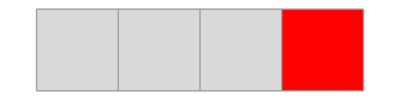

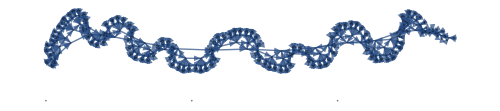
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"AAAB"->"BA",""->"A"},"BBB",500,SSSMax->500,SSSSize->100,NetSize->500,VertexLabels->Position[Automatic,Tooltip]];
```

```mathematica
CheckDimension[LeastUsedRulePositions[sss]]
```

{1D,{9,0,13,40/9},4 | 8 | 13 | 17 | 21 | 26 | 30 | 34 | 40
4 | 5 | 4 | 4 | 5 | 4 | 4 | 6 | 4,4 | 8 | 13 | 17 | 21 | 26 | 30 | 34 | 40 | 44 | 48 | 53 | 57 | 61 | 66 | 70 | 74 | 80 | 84 | 88 | 93 | 97
4 | 5 | 4 | 4 | 5 | 4 | 4 | 6 | 4 | 4 | 5 | 4 | 4 | 5 | 4 | 4 | 6 | 4 | 4 | 5 | 4 | }

```mathematica
CheckDimension[MaxStateLengthPositions[sss]]
```

{1D,{1,2,5,13},12
13,4 | 8 | 12 | 25 | 38 | 51 | 64 | 77
4 | 4 | 13 | 13 | 13 | 13 | 13 | }

```mathematica
CheckDimension[DistanceLastPositions[sss]]
```

Part::partw: Part 498 of {2,1,2,0,3,2,3,3,4,3,«487»} does not exist.

Part::take: Cannot take positions 493 through 489 in {2,2,2,1,2,2,2,1,2,2,«490»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

$Aborted

```mathematica
CheckDimension[DistanceTally[sss]]
```

Part::partw: Part 498 of {2,1,2,0,3,2,3,3,4,3,«487»} does not exist.

{failed,1 | 5 | 11 | 19 | 35 | 57 | 97 | 137 | 177 | 217 | 257 | 297 | 337 | 377 | 416 | 453 | 483 | 493 | 496
4 | 6 | 8 | 16 | 22 | 40 | 40 | 40 | 40 | 40 | 40 | 40 | 40 | 39 | 37 | 30 | 10 | 3 | 
2 | 2 | 8 | 6 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | -7 | -20 | -7 |  | 
0 | 6 | -2 | 12 | -18 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -5 | -13 | 13 |  |  | 
6 | -8 | 14 | -30 | 18 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -4 | -8 | 26 |  |  |  | 
-14 | 22 | -44 | 48 | -18 | 0 | 0 | 0 | 0 | -1 | 1 | -4 | -4 | 34 |  |  |  |  | 
36 | -66 | 92 | -66 | 18 | 0 | 0 | 0 | -1 | 2 | -5 | 0 | 38 |  |  |  |  |  | 
-102 | 158 | -158 | 84 | -18 | 0 | 0 | -1 | 3 | -7 | 5 | 38 |  |  |  |  |  |  | 
260 | -316 | 242 | -102 | 18 | 0 | -1 | 4 | -10 | 12 | 33 |  |  |  |  |  |  |  | 
-576 | 558 | -344 | 120 | -18 | -1 | 5 | -14 | 22 | 21 |  |  |  |  |  |  |  |  | 
1134 | -902 | 464 | -138 | 17 | 6 | -19 | 36 | -1 |  |  |  |  |  |  |  |  |  | 
-2036 | 1366 | -602 | 155 | -11 | -25 | 55 | -37 |  |  |  |  |  |  |  |  |  |  | 
3402 | -1968 | 757 | -166 | -14 | 80 | -92 |  |  |  |  |  |  |  |  |  |  |  | 
-5370 | 2725 | -923 | 152 | 94 | -172 |  |  |  |  |  |  |  |  |  |  |  |  | 
8095 | -3648 | 1075 | -58 | -266 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-11743 | 4723 | -1133 | -208 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | }

#### Interesting:

Look at last half after, say 100 steps.  count backwards as long as some pattern exists.  Take previous non-pattern stuff, see if it’s an exact repeat!  Pseudo-repetition => set “Verdict”

<|Index→362130,QCode→31430343,RuleSet→{AA→,BA→,→ABA}|>


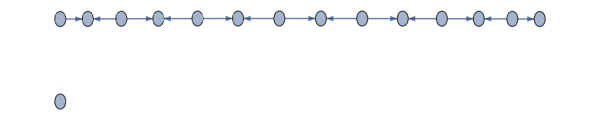
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss=SSS[{"AA"->"","BA"->"",""->"ABA"},"ABAA",50,SSSMax->20,SSSSize->100,NetMax->15,NetSize->600];
```

```mathematica
sss["RulesUsed"]
```

{1,2,2,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}

```mathematica
ssst0=SSS[{"AB"->"BAA",""->"AB"},"",750,SSSSize->Small,SSSMax->15,NetSize->Medium,VertexLabels->Placed[Automatic,Tooltip]];
Column@{CheckDimension@LeastUsedRulePositions[ssst0],CheckDimension@MaxStateLengthPositions[ssst0],CheckDimension@DistanceTally[ssst0],CheckDimension@DistanceLastPositions[ssst0]}
```

```mathematica
ssst0["RulesUsed"]
```

<|Index→50467525,QCode→34243313433,RuleSet→{AB→BAA,→ABAA}|> : {exp2,exp2,3D,failed} - OK